```mathematica
(* Oka's data *)
data ={{0.8,1.75},{1.1,1.65},{1.3,1.6},{1.5,1.5},{1.8,1.1},{2.2,0.6}};
```

```mathematica
(* Fit of modified Cam-Clay*)
modCamClay=NonlinearModelFit[data,{a √(p(b-p)),b>2.2},{a,b},p];
(* Fit of Cam-Clay*)
camClay=NonlinearModelFit[data,{a p Log[b/p]},{a,b},p];
```

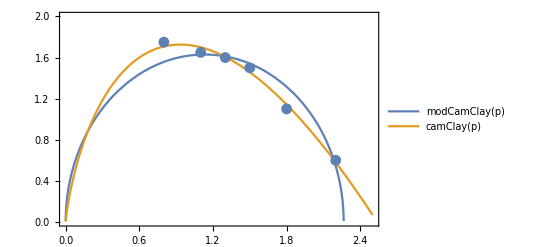

```mathematica
Show[
Plot[{modCamClay[p],camClay[p]},{p,-1,2.5},PlotLegends->"Expressions"], (* Plot fits *)
ListPlot[data], (* Plot data *)
Frame->True,
PlotRange->{{0,2.5},{0,2}}
]
```

```mathematica
(* Show fit results in human readable form *)
Normal[camClay]
```

1.8493 p Log[2.53708/p]

```mathematica
Normal[modCamClay]
```

1.43882 √((2.26473-p) p)

```mathematica
Maximize[{camClay[x],x>0},x]
```

{1.72602,{x→0.933339}}

```mathematica
Maximize[{modCamClay[x],x>0},x]
```

{1.62927,{x→1.13236}}

```mathematica
dataNormalized = Table[{data[[i,1]]/1.62,data[[i,2]]/2.5},{i,Length[data]}]
```

{{0.493827,0.7},{0.679012,0.66},{0.802469,0.64},{0.925926,0.6},{1.11111,0.44},{1.35802,0.24}}